```mathematica
speed[p_]:=Log10[p] p^1.1+p-1
```

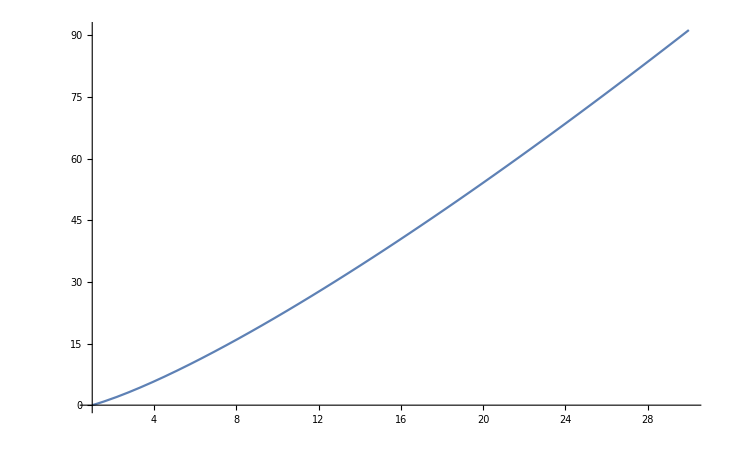

```mathematica
Plot[speed[p],{p,1,30}]
```

```mathematica
Series[speed[p],{p,15,1}]
```

37.1282+3.26543 (p-15)+O[p-15]^2

```mathematica
Normal[37.12817725833908+3.2654348333723484 (p-15)+O[p-15]^2]
```

37.1282+3.26543 (-15+p)

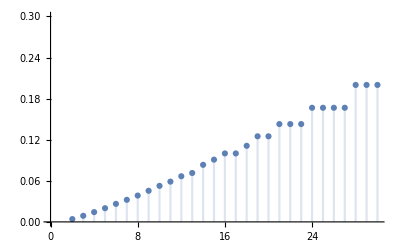

```mathematica
DiscretePlot[1/Ceiling[400/speed[p]],{p,2,30},ImageSize->Full,PlotRange->{0,0.3}]
```

```mathematica
Maximize[{1/Ceiling[400/speed[p]]/Log[p],p>21},p,Integers]
```

{0.052443,{p→24}}